# A Mathematica NURBS (Non-Uniform Rational B-Splines) Package and Its Applications

Author: Liutong Zhou
Columbia University

## Chapter 3 B-Spline Curves and Surfaces

All the customized functions we showed here are included in the package “NURBS”

```mathematica
Needs["NURBS`"]
```

Package NURBS.wl By Liutong Zhou, Version 1.0
Created on Nov. 25 2016
Last Updated on Dec 11 2016

User-accessible functions:
NDegreePowerBasis,Bernstein, MyBezierCurve, PlotBezierCurve, RationalBezierCurve, PlotRationalBezierCurve,BezierSurface,PlotBezierSurface,
RationalBezierSurface,PlotRationalBezierSurface, MyBSplineBasis, MyBSplineCurve, PlotBSplineCurve, DBSplineCurve, MyBSplineSurface, PlotBSplineSurface

Type ?functionname to see usage information

## 3.2 Definition of B-Spline Curves (Uniform)

A p-th degree B-Spline Curve is defined by

C(u)=∑_(i=0)^n N_(i,p)(u)P_i, for a≤ u≤b

where P_is are the control points and N_(i,p)(u) s are the p-th degree B-Spline Basis defined in Section 2.2, and the knots are

U={0,...,0,u_(p+1),...,u_(m-p-1),b,...,b}

```mathematica
?MyBSplineCurve
```

MyBSplineCurve[points,U,p,u] returns the parametric form of the p degree B-Spline Curve defined by knot vector U

```mathematica
?PlotBSplineCurve
```

PlotBSplineCurve[points,U,p] plots the p degree B Spline curve defined by knot vector U

### Example: B-Spline Curve of different degrees

```mathematica
points=RandomInteger[{0,10},{6,3}];
Table[PlotBSplineCurve[points,{0,0,0,0,0.4,0.5,0.6,1,1,1,1,1,1,2},i],{i,0,3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
s
```

### Example: A cubic B-Spline Curve

Claim: If n=p and U={0,...,0,1...,1} then C(u) is a Bezier Curve
Lets prove the claim using some plots.

```mathematica
U={0,0,0,0,1,1,1,1};points=RandomInteger[{0,5},{4,2}];Graphics[{BSplineCurve[points,SplineKnots->U],Blue,Line[points],{Red,PointSize[Medium],Point[points]}}]
```

-Graphics-

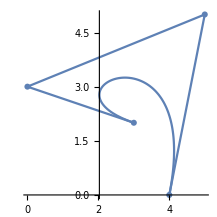

```mathematica
PlotBezierCurve[points]
```

The parametric form of this B-Spline curve

```mathematica
MyBezierCurve[points,u]
```

{4+3 u-18 u^2+14 u^3,u (15-21 u+8 u^2)}

Show by graph that MyBSplineCurve returns the same parametric function as does the built-in BSplineFunction.

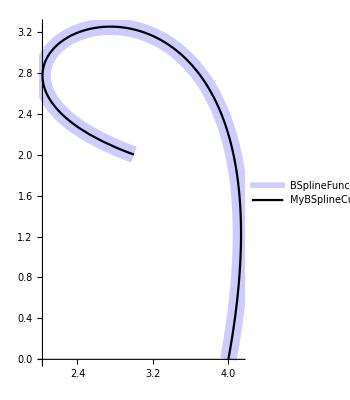

```mathematica
ParametricPlot[{BSplineFunction[points]@u,MyBSplineCurve[points,U,3,u]},{u,0,1-0.0001},PlotStyle->{Directive[Blue,Thickness[0.03],Opacity[0.2]],Directive[Thin,Black]},PlotLegends->"Expressions"]
```

### Example: End Point Interpolation

B-Spline Curve passes through the first and the last points {C(0),C(1)}={P_0,P_1}

```mathematica
BSplineFunction[points]/@{0,1}
points[[{1,-1}]]
BSplineFunction[points]/@{0,1}==points[[{1,-1}]]
```

{{2.,3.},{4.,3.}}

{{2,3},{4,3}}

True

## 3.3 Derivatives of B-Spline Curves (Uniform)

Derivation of the derivative(s) of the B-Spline Curve is given from equation (3.3) to equation(3.6) in the NURBS Book

C^(k)(u)=∑_(i=0)^n (N_(i,p))^(k)(u)P_i

And

C'(u)=∑_(i=0)^(n-1) N_(i,p-1)(u)Q_i, where Q_i=p (P_(i+1)-P_i)/(u_(i+p+1)-u_(i+1))

This tells us that C’(u) is a (p-1)-th degree B-Spline Curve

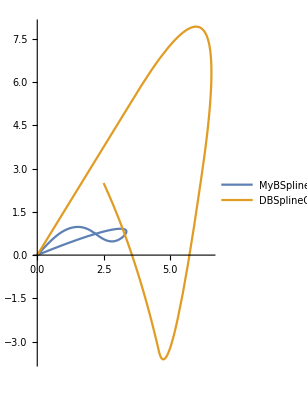

```mathematica
ParametricPlot[{MyBSplineCurve[{{0.5,0.5},{1,1},{2,1},{3,0},{4,1.5}},{0,0,0,2/5,3/5,4/5,1,1,1},3,u],DBSplineCurve[{{0.5,0.5},{1,1},{2,1},{3,0},{4,1.5}},{0,0,0,2/5,3/5,4/5,1,1,1},3,u]},{u,0,1},PlotLegends->"Expressions",PlotRange->All]
```

## 3.4 Definition of B-Spline Surfaces

The parametric function of B Spline Surfaces is

S(u,v)=∑_(i=0)^n ∑_(j=0)^m N_(i,p)(u)N_(j,q)(v) P_(i,j)

```mathematica
points={{{0,0,0},{1,0,0},{2,0,0}},{{0,1,1},{1,1,1},{2,1,1}},{{0,2,0},{1,2,0},{2,2,0}}};
U={0,2/5,3/5};V={0,0,0};
PlotBSplineSurface[points,U,V,2,2]
```

-Graphics3D-